# Regression modelling of precision matrix

## Full rank case

### Generate data

```mathematica
(* Batch dimension is last one *)
n=2;
e=0.01;
cov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,cov];
pdf[x_,y_]=PDF[normal,{x,y}];
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
(* center the data *)
Xc=Mean[Transpose@X];
X=Transpose[#-Xc&/@Transpose[X]];
wt = {{1,1}}; (* true w *)
w0={{2,1}}; (* initial w *)
Y=Dot[wt, X];
XY = X~Join~Y;
grad[w_]:=2(w.X-Y).Transpose[X]/dsize;
loss[w_]:=Module[{error},
error=(w.X-Y);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Loss at w0 ",loss[w0]];
Print["Grad at w0 ",grad[w0]];
covE=X.Xᵀ/dsize; 
covE2=X.Xᵀ/(dsize-1); (* unbiased estimate *)
(* sanity checks *)
Print["True cov ",MatrixForm@cov];
Print["Empirical cov ", MatrixForm@covE];
Print["Empirical mean ", Mean@Transpose@X]
```

Loss at w0 1.03475

Grad at w0 {{2.06949,2.05021}}

True cov (1 | 0.99
0.99 | 1)

Empirical cov (1.03475 | 1.02511
1.02511 | 1.03619)

Empirical mean {-2.45359×10^-17,1.98286×10^-16}

### Modified Cholesky decomposition of covariance matrix

Use lower diagonal Cholesky as in page 64 of Pourahmadi

```mathematica
Ch=CholeskyDecomposition@covE//Transpose;
Ch//MatrixForm
```

(1.01722 | 0.
1.00775 | 0.143648)

```mathematica
Ch.Chᵀ==covE
```

True

```mathematica
Subscript[D, 1]=DiagonalMatrix@Diagonal@Ch
```

{{1.01722,0.},{0.,0.143648}}

```mathematica
L=Ch.Inverse[Subscript[D, 1]];
L//MatrixForm
```

(1. | 0.
0.990685 | 1.)

```mathematica
L.Subscript[D, 1].Subscript[D, 1].Lᵀ==covE
```

True

### Modified Cholesky decomposition of precision matrix

```mathematica
T=Inverse@L;
T//MatrixForm
```

(1. | 0.
-0.990685 | 1.)

```mathematica
Inverse[covE]==Tᵀ.Inverse[Subscript[D, 1].Subscript[D, 1]].T
```

True

#### Calculate residual variances

```mathematica
(* get decorrelated representation *)
Xnew=T.X;
```

```mathematica
Xnew.Xnewᵀ/dsize//MatrixForm
```

1/1000 T.{{-0.540758,-0.719989,0.440679,-1.02046,-1.22784,0.826259,-0.204872,0.138596,0.588065,-0.584474,0.530921,-0.197501,-0.379076,-0.769369,-0.499088,-0.927036,1.00203,0.878862,0.966474,-0.111012,-0.116512,-0.739946,-0.763847,0.972812,1.50059,0.166243,-0.547528,-0.346623,0.709272,-1.63116,0.644733,-0.646289,-0.685533,-1.09104,-1.36413,-0.462924,-1.12345,-1.71289,0.275004,0.774876,1.17307,-1.36316,0.254504,0.945845,-0.548839,-1.07513,-0.252544,-0.474844,-0.478845,-1.12223,-2.40867,0.253743,-2.16591,0.928756,1.22188,-0.409512,0.528404,0.375373,-1.08802,-1.29175,0.306633,-1.84721,-0.266933,1.37644,0.624694,0.206709,0.245307,0.253316,0.32939,-0.293979,0.1631,-0.225423,2.16308,1.03993,-0.899383,-0.11186,-0.955944,-0.943715,-1.06013,-0.370852,-0.901576,0.215836,0.547406,-2.37454,0.315035,2.37815,0.661353,-1.04145,-0.670203,0.513476,0.653844,-0.649598,2.31136,-0.439032,0.799647,0.0659168,-0.194646,-0.600617,0.334741,1.32211,0.810906,-0.31554,2.14601,-0.378488,0.954037,-0.317715,2.08411,0.605125,-0.475508,0.495978,-0.340012,-0.238889,-0.316902,1.42351,-1.92262,-0.865331,0.232559,2.04416,1.76171,-0.529961,1.40276,0.241017,0.489346,0.570437,-1.4069,1.30393,-0.822893,-1.19888,0.863062,-1.31378,-1.32418,-1.32838,0.362025,-0.35835,-0.332774,1.03155,-1.70664,-0.87199,-0.177919,1.85968,0.994008,-0.547302,0.134808,-0.483388,-0.107018,-0.140439,0.576441,-0.0205363,-0.986218,1.2235,-0.249652,3.13355,0.0889763,-0.694033,0.981019,0.235557,0.817558,1.27865,-0.318083,-0.858163,0.497426,-0.367568,-0.126896,2.24762,-0.312902,-0.846965,0.804273,-1.659,0.0403862,1.19507,-1.22872,-2.28363,1.60106,0.829197,-1.6185,-1.02559,0.704873,1.33183,-1.31649,1.43904,-0.993152,-2.64886,0.357951,-0.806391,-1.4418,0.230737,-1.25687,0.0737753,0.94641,1.52463,0.499413,-1.00345,0.809651,-1.46163,-0.34734,0.259622,-0.61832,1.03505,-0.956807,0.0693905,0.68145,-0.618106,-1.39598,-0.25214,-0.313438,1.11894,-0.440144,-0.455465,-1.18996,0.424441,1.98402,-1.84529,-0.00736693,0.942643,-1.11102,-0.810967,-0.974077,1.14416,-0.06965,1.70702,-0.423441,-0.727951,0.662038,0.758945,-1.40926,-0.124364,-0.6022,0.641503,-1.04183,0.486079,1.17088,-1.17784,0.173045,-0.131784,-0.366131,2.51709,-0.7559,-0.315498,0.148481,0.0820289,-0.491608,1.06485,-0.0250617,-0.185731,0.664209,1.56626,-0.421761,0.371309,0.539241,0.959168,0.649345,-0.291175,-0.281427,-0.373656,-1.07861,1.14762,0.279876,0.756897,-0.231376,0.0845706,0.171406,0.11989,0.325136,-2.13494,-1.46663,-0.279677,-0.193207,1.4369,-0.200857,-1.4574,0.487873,0.136035,-0.144441,-0.573785,0.0837273,0.833885,0.209949,0.235467,-1.17208,-0.692019,0.145794,1.15706,0.00191417,-1.6184,0.353187,-0.311455,-0.529265,0.707048,0.362602,-0.6024,2.21072,-0.606144,2.06816,1.40015,0.964095,1.62373,1.20411,0.616985,-0.918879,-0.975734,-0.0897206,1.11392,0.017133,-0.469944,0.506098,-1.47229,0.4276,0.0408859,-0.639204,-1.38414,1.16423,0.248766,-1.02171,1.58332,0.623585,-0.620537,-0.687978,0.25232,-1.25848,0.645153,2.02427,-0.181846,-0.482484,-0.36247,0.031648,-0.603738,-0.581237,-0.629604,-1.3345,0.129122,-1.36298,-1.61546,1.1872,1.1155,0.261964,-0.323025,-0.166164,-1.85985,-0.775312,-0.542723,-0.431589,1.47728,0.717049,1.14043,-1.10964,-0.823818,-0.500935,-0.500729,0.195735,-0.266532,-0.737234,-0.0639798,-0.589609,0.642963,-0.120986,0.427997,1.33045,-1.30136,-0.914925,-0.850096,0.481782,1.72362,0.592653,0.153885,1.41802,0.974214,0.313887,0.273804,0.326682,-0.484196,-0.681745,1.82666,0.256663,0.956847,0.895952,-0.26587,-0.0790881,-0.659142,0.0874621,0.164337,-0.970817,-1.1755,-2.33683,0.856763,-0.266945,2.24851,0.199753,-0.485796,0.815072,-0.759933,0.995372,1.15361,0.970674,-0.221652,0.879037,1.16391,-0.0653951,0.688076,0.86945,-0.198167,-0.746433,-1.15131,-0.378831,0.603004,-0.104923,0.892359,0.140151,0.655119,0.0234816,0.582958,-1.05766,0.508353,-0.460459,-0.531974,-0.71072,-0.597021,0.465402,0.15456,-0.682609,-0.119591,0.758364,-0.00639246,-1.19452,-1.10263,2.48341,-1.33182,0.285678,-1.42174,-2.0854,-0.868019,-0.459084,0.40392,-0.681395,0.0102097,0.776164,-0.620768,0.542925,0.800172,0.41925,-1.18883,-0.551218,1.87841,0.365955,0.458282,-1.48347,-1.18544,-1.04856,-0.529458,-0.688867,0.297539,-1.67553,-0.130106,0.419722,0.0399401,-0.403402,-1.16372,1.4634,0.109708,1.51255,0.075556,4.52326,1.78149,-0.289227,-2.57143,0.209462,-1.52363,-0.00849605,0.195526,0.825294,-0.727943,0.982865,-0.544948,-0.365043,-0.0520782,0.850195,0.539357,0.94997,0.706682,-0.997641,1.00025,-0.893705,0.583217,-0.17842,-1.08307,-0.35893,0.392325,-0.608962,-0.183757,-0.177936,0.995456,2.81199,-0.0219958,-2.08895,0.0443117,-0.472582,-1.52764,0.529294,-0.210478,1.88449,-0.23046,-0.444948,1.22881,-0.370484,-1.89305,-0.152373,-0.949561,-2.03937,1.49832,-2.28204,1.14344,-0.311068,0.627159,-0.546882,0.344277,1.30895,-0.374919,-0.381358,-0.971911,1.07683,0.761305,1.26126,-1.33159,0.208396,-1.90809,1.25527,-0.289267,-0.630148,-2.95759,-0.478441,-1.0094,0.279797,2.05573,-1.07991,0.109324,1.46546,-1.45426,0.599226,-0.357858,0.0576963,-0.240407,-0.209411,-1.63273,2.02917,1.46818,-0.29924,1.25168,-0.304696,-1.54281,-0.537026,-0.229912,0.353404,-0.711841,-0.183281,0.540492,-0.926026,0.0186442,0.63196,-0.3461,0.702649,1.44393,0.572178,-0.764145,0.796747,1.69328,-0.961003,-0.251333,-0.863308,-1.43703,1.75218,-0.203872,0.41763,-0.911893,1.00414,-0.476833,-1.98645,-1.43616,-0.638996,2.01133,0.478505,-1.61331,-2.12961,1.33674,-1.4692,0.997353,-1.77734,0.650334,0.439676,1.05135,-0.495144,-0.834001,-1.78755,0.403253,0.948826,0.553445,-0.328563,0.976804,-0.589484,1.06511,0.856244,-0.221689,1.31832,1.16403,0.332917,0.442943,0.548734,-0.19168,-0.862992,1.29658,-2.54006,-0.10716,1.10117,1.90445,-0.161598,1.00296,-0.365423,-0.0482304,0.696981,0.343484,0.471954,-1.08354,-1.51934,0.235671,0.741672,0.940426,-0.829133,-0.29703,-1.73325,-1.99484,2.35083,-0.381656,-0.845181,1.99042,0.19997,0.679431,0.220378,-0.00967752,1.32085,-0.0609304,-0.7431,0.300509,-0.850986,0.453031,-0.735767,1.35349,-0.582068,-0.694144,-1.40325,0.0656408,-0.264415,-0.831596,-0.0414745,2.42829,-0.958198,0.566418,-0.761158,-0.43446,0.632689,-1.49595,-0.735166,-0.247004,1.96838,2.6208,-0.136771,0.468879,-0.341733,0.164422,-0.780868,-0.512892,1.0502,0.576608,-0.319297,0.859901,-0.317506,-1.21691,-2.23541,1.87939,-0.820526,-0.397805,-1.22477,0.613407,1.23038,0.775107,-0.541002,1.77024,0.383889,0.244048,-1.57528,-0.732916,2.03483,-0.000937103,-0.254694,-2.00911,-0.0453224,-0.838692,0.391236,-1.76522,1.37485,-0.152184,-1.86916,-1.09049,-2.06233,-2.37494,-0.72863,-0.333157,-0.483787,-0.0671703,-0.660852,-0.873891,0.632589,0.463925,-0.0229525,-1.43816,-0.00334895,-0.0202455,1.10935,-0.454086,-2.04948,0.92497,0.254312,-0.860709,-0.440897,0.420621,-1.6157,1.33811,0.00513606,0.318583,-0.0657717,-0.304176,-0.0186317,0.384739,0.429731,0.154347,-1.63695,0.303282,-0.126199,0.726911,1.80099,1.33544,0.692395,0.0698152,-0.302616,1.05667,-0.788015,-1.70931,0.709411,0.476083,-1.76692,0.137214,0.656341,-0.608064,1.55477,-0.0941836,0.358686,1.08093,0.402832,1.22757,-2.07719,1.47313,-0.106994,-0.27172,1.44194,0.483793,0.263142,-0.469116,0.421988,0.820586,-0.530256,-1.72271,-0.876419,-0.616489,0.503746,0.507564,-1.56987,0.119996,-1.79827,-1.48864,0.626463,-0.282062,3.04212,0.313997,-1.14865,0.803886,2.29729,-0.283189,0.572368,-0.309205,0.303298,0.083353,-0.331066,-0.0149485,-2.739,0.120353,0.693644,0.323978,-0.869702,-0.273325,0.68011,-0.991274,-0.72424,1.63537,0.9651,-0.108646,-0.515244,-0.832408,0.49543,-0.515035,-1.38775,0.909078,-0.543211,0.113388,1.25479,-0.407993,0.27685,1.74294,0.195862,-1.22681,-0.144866,-1.5379,0.718839,-1.1504,-0.464909,-0.353736,-0.10635,-1.34858,-1.28793,-0.0697771,0.155867,-0.731016,0.61276,-0.343597,-1.59369,1.45859,0.0963107,1.09551,1.68146,0.903277,-0.175888,0.519942,-0.821547,-0.0522871,-1.40956,-0.204791,0.199131,0.537153,-0.535384,0.216105,1.35984,0.351922,0.977452,0.725852,-0.0309377,0.140413,1.04645,-0.476419,-1.20453,-1.20505,0.162571,-0.0158898,-1.54676,-0.595191,-0.691904,0.655926,0.585395,0.298486,-1.62298,-1.59751,-0.538756,-0.338798,0.45496,0.454656,0.704345,-0.335726,1.78642,0.769138,0.414198,1.47653,1.44668,-1.09701,-0.481734,-1.10025,1.3283,2.06653,-2.2707,-1.93383,-0.0370317,0.774665,0.915713,-0.372523,-0.215365,-0.782571,0.787254,-0.632945,0.741525,1.38452,-1.29914,-0.744143,-2.19891,-0.563728,1.06934,-0.935257,-0.0601614,-0.544756,-0.59216,1.01847,-0.990259,1.09557,-0.447379,0.161147,0.295146,0.0316905,-0.112667,-0.80993,-0.0135661,-1.07613,-1.1477,-1.07793,-0.360334,-0.899688,1.36964,0.0544331,1.39685,-0.918876,0.518452,0.840705,-0.373962,-0.789857,0.246213,1.18997,1.31138,0.420073,0.206908,2.90459,0.771643,-0.145681,0.427121,-0.0274139,1.4459,1.68011,0.343419,0.231612,0.913871,-1.19757,0.443829,1.8776,0.129796,1.08271,1.04823,-0.306583,1.08619,-1.14331,0.162688,1.58191,-2.28173,1.84998,-0.409324,0.934317,0.0261892,0.275177,0.990514,-0.257319,1.04072,0.157245,0.832994,-0.025745,0.740577,1.77754,2.32725,0.774201,-0.785932,1.241,0.414369,0.128131,1.1174,-2.30562,1.29455,-0.370354,0.965837,-1.00292,1.37689,-1.45106,0.114804,-0.701539,1.02428,-2.59416,0.856536,1.57441,0.742323,1.05186,-0.152397,0.730973,-0.571256,0.337425,-0.420855,-0.326236,-0.978611,-0.687526,0.033698,0.469466,-1.02697,0.920453},{-0.632293,-0.762896,0.428367,-1.19216,-1.45501,0.568919,-0.251835,-0.0797666,0.590653,-0.454022,0.512768,-0.134572,-0.160666,-0.772513,-0.437854,-0.784394,1.11977,0.826148,0.674065,-0.142424,-0.146945,-0.610361,-0.935135,0.784383,1.81779,0.044516,-0.775245,-0.168532,0.40865,-1.32752,0.84361,-0.673093,-0.672624,-1.11103,-1.37051,-0.26646,-1.0561,-1.62522,0.35627,0.836527,1.14917,-1.33785,0.429732,0.715027,-0.59567,-1.05521,-0.348886,-0.470417,-0.411738,-1.31836,-2.39375,0.12608,-2.09025,0.847852,1.04846,-0.572187,0.337235,0.218856,-1.02038,-1.34614,0.297693,-2.05155,-0.202495,1.47877,0.417287,-0.00287212,0.257785,0.202047,0.220604,-0.252813,0.186755,-0.384025,2.01038,1.1105,-1.05732,-0.117018,-0.888961,-0.874242,-1.14523,-0.336232,-0.734674,0.304334,0.565436,-2.30734,0.247084,2.51107,0.770224,-0.746074,-1.02004,0.587467,0.743238,-0.642263,2.42782,-0.360911,0.808878,0.0928624,-0.0815383,-0.508681,0.434133,1.65141,0.518134,-0.385657,2.13722,-0.286656,0.867619,-0.256698,1.82321,0.649918,-0.441205,0.328494,-0.231217,-0.135485,-0.350534,1.48294,-1.96637,-0.762238,-0.217976,1.90111,1.5238,-0.667589,1.57212,0.38979,0.364325,0.527359,-1.41348,1.00125,-0.777223,-1.19114,0.674615,-1.40946,-1.26228,-1.50396,0.352147,-0.215226,-0.402507,0.891323,-1.78537,-0.761048,0.153517,1.88211,0.973405,-0.635751,0.203787,-0.554564,0.130414,-0.255347,0.302611,0.150107,-0.842483,1.18118,-0.474362,3.41522,0.120248,-0.658401,0.670218,0.244002,0.981813,1.21936,-0.428912,-0.63702,0.423689,-0.359065,-0.352874,2.05179,-0.419433,-0.742867,0.579464,-1.61537,-0.0360063,1.29269,-1.21205,-2.30072,1.67848,0.950514,-1.48459,-1.19039,0.787559,1.28431,-1.25019,1.37645,-0.957366,-2.5503,0.0499998,-0.868848,-1.38705,0.299116,-1.27853,0.0520802,0.93542,1.49933,0.495912,-0.992033,0.767281,-1.42251,-0.277023,0.477864,-0.464748,0.939137,-1.18528,0.057589,0.841732,-0.607381,-1.54394,-0.00829431,-0.505809,1.03716,-0.368785,-0.401725,-1.08572,0.174741,1.91283,-1.81344,-0.13809,0.859559,-1.02356,-0.776435,-0.881934,1.30974,-0.109523,1.8347,-0.323751,-0.933845,0.548863,0.833796,-1.26625,-0.238048,-0.761537,0.690783,-1.18821,0.518794,1.1494,-1.42002,0.287486,-0.119603,-0.454585,2.40943,-0.718769,-0.39012,0.196252,-0.0433766,-0.486131,0.622992,0.145747,-0.383133,0.559119,1.57915,-0.623646,0.239645,0.657674,0.872872,0.673375,-0.0999528,-0.184085,-0.437975,-1.14198,1.32985,0.0333824,0.575557,-0.29619,0.0665193,0.400738,0.523242,0.274076,-2.06289,-1.48302,-0.585073,-0.168795,1.64613,-0.511854,-1.20005,0.490958,0.0470224,-0.0301626,-0.441482,-0.0815761,0.992474,-0.0988361,0.475935,-1.16675,-0.96026,0.191648,1.06764,-0.14061,-1.63864,0.517164,-0.232376,-0.5627,0.630159,0.511373,-0.670372,2.20458,-0.407897,1.97232,1.55017,1.08875,1.42467,1.49316,0.518348,-0.863751,-1.01841,-0.191837,0.798442,0.233766,-0.463034,0.513396,-1.49129,0.507963,0.124711,-0.499462,-1.31042,1.11338,0.291748,-1.30851,1.49518,0.62608,-0.749857,-0.648358,0.0682372,-0.965782,0.708556,1.98977,-0.14925,-0.161929,-0.438671,0.030733,-0.291855,-0.411313,-0.297351,-1.33558,-0.103942,-1.19039,-1.60476,1.19387,1.3359,0.404208,-0.48102,-0.0819159,-1.95333,-0.930213,-0.46118,-0.472012,1.6108,0.685556,1.43447,-1.20883,-0.649584,-0.281274,-0.571621,0.225348,-0.139532,-0.786414,-0.0760646,-0.518548,0.805005,-0.0416059,0.531788,1.31098,-1.32454,-0.791048,-1.06462,0.342201,1.61641,0.54989,0.0341115,1.50911,1.27471,0.27182,0.275017,0.199427,-0.405512,-0.836354,1.79653,0.327754,0.918045,0.907471,-0.155157,0.0251124,-0.592435,-0.235079,-0.0261628,-0.956679,-1.03912,-2.20903,0.881513,-0.0798338,2.37951,-0.0026017,-0.620667,0.574328,-0.910842,0.9214,1.1583,0.81998,-0.193809,0.578498,0.924693,-0.179211,0.713097,0.659444,-0.389591,-0.867421,-1.11288,-0.195793,0.67262,-0.107284,0.848723,-0.0212689,0.530548,-0.0874657,0.627442,-0.928773,0.72181,-0.463616,-0.491255,-0.748081,-0.426006,0.453593,0.404015,-0.558234,-0.10965,0.795695,-0.185371,-1.12494,-1.1182,2.36544,-1.28368,0.214238,-1.37819,-2.1691,-0.989986,-0.396404,0.438259,-0.852416,-0.0500048,0.518878,-0.565587,0.522211,0.865997,0.509721,-1.07807,-0.572659,1.87226,0.307011,0.378935,-1.52026,-1.30898,-1.06675,-0.50271,-0.743908,0.133365,-1.71716,-0.00180316,0.473552,-0.120554,-0.0678858,-1.15814,1.44151,0.163343,1.35825,-0.0658725,4.48756,1.72672,-0.147302,-2.40723,-0.0471602,-1.68721,0.0525157,0.237813,0.761064,-0.539701,0.90077,-0.447618,-0.353412,-0.0423247,0.708021,0.471137,0.712124,0.482131,-1.10679,1.18873,-0.732866,0.707329,-0.0120124,-0.852722,-0.557702,0.693658,-0.524409,-0.275352,-0.089991,1.04649,3.04921,0.347319,-1.95322,-0.297532,-0.438292,-1.67787,0.630981,-0.020793,1.6825,-0.204619,-0.450154,1.34307,-0.570385,-1.9056,-0.349541,-0.872513,-2.08279,1.67216,-2.22672,1.02366,-0.359474,0.555367,-0.50079,0.391735,1.29417,-0.33398,-0.380791,-0.916664,0.990486,0.730129,1.1014,-1.33725,0.327071,-1.85129,0.993602,-0.382962,-0.905399,-3.12246,-0.449552,-0.666546,0.34624,2.15777,-1.1183,0.218643,1.49281,-1.47966,0.529684,-0.590086,0.157353,-0.481754,-0.052631,-1.77016,1.8593,1.41471,-0.307846,1.08482,-0.283973,-1.6479,-0.421891,-0.189842,0.279302,-0.646006,-0.196174,0.300766,-1.05003,-0.0700513,0.866766,-0.172247,0.781752,1.50107,0.815523,-0.550509,0.803932,1.56494,-1.03392,-0.142033,-1.04733,-1.41303,1.67503,-0.241704,0.539016,-0.772018,1.2288,-0.460472,-1.71786,-1.4077,-0.559615,2.09133,0.698118,-1.5859,-2.03066,1.29147,-1.54494,0.867965,-1.94498,0.777822,0.386242,1.4421,-0.5629,-1.1475,-1.83558,0.421516,0.87345,0.467897,-0.17754,1.0866,-0.170548,1.23694,0.845047,-0.270736,1.38632,1.05368,0.308856,0.695691,0.586651,-0.084682,-0.646623,1.19552,-2.67813,-0.133212,1.07737,1.8079,-0.13895,0.985556,-0.331093,-0.0929631,0.688572,0.26612,0.524452,-1.42098,-1.71534,0.167649,0.56393,0.870856,-0.574355,-0.403028,-1.55371,-1.99463,2.4532,-0.52375,-0.75992,1.71755,0.0908289,0.681803,0.299932,0.0505824,1.40006,-0.066219,-0.672302,0.480089,-0.674796,0.683532,-0.669061,1.45996,-0.467456,-0.761338,-1.55278,-0.263802,-0.413897,-0.807897,0.0382359,2.62411,-0.800007,0.535052,-0.688996,-0.403453,0.408897,-1.50435,-0.832004,-0.20066,1.77265,2.80158,-0.149934,0.634687,-0.319076,0.345949,-0.510184,-0.594766,0.971599,0.582735,-0.362625,1.02719,-0.519771,-0.902644,-2.16075,2.19972,-0.691299,-0.452574,-1.33839,0.632178,1.23415,0.861372,-0.271407,1.69016,0.238185,0.121478,-1.36808,-1.11432,2.0512,0.314408,-0.44193,-1.98022,0.0355391,-0.699429,0.451792,-1.71752,1.31958,-0.0802151,-1.87587,-1.32211,-2.00067,-2.39948,-0.840758,-0.447564,-0.518897,-0.113351,-0.853433,-0.946077,0.52405,0.60739,0.280273,-1.34166,0.0375521,-0.0605326,1.14014,-0.28802,-1.91601,0.570475,0.261756,-0.667937,-0.259641,0.266888,-1.68061,1.40916,0.148507,0.518549,-0.070361,-0.260605,-0.102872,0.462553,0.703234,0.102713,-1.72445,0.0946162,-0.157495,0.659066,1.68417,1.27118,0.757153,0.246534,-0.0720797,1.3197,-0.885533,-1.62953,0.491282,0.31076,-1.76026,0.288924,0.702796,-0.696809,1.4324,-0.0348591,0.393628,1.03298,0.495783,1.40592,-2.18709,1.82293,-0.292088,-0.135654,1.67718,0.477714,-0.00475912,-0.720884,0.270846,0.827278,-0.358414,-1.59861,-0.787586,-0.686748,0.521756,0.581539,-1.69107,-0.00182435,-1.7757,-1.48558,0.518503,-0.055819,3.17928,0.274664,-0.917271,0.452897,2.30633,-0.0521652,0.917954,-0.492521,0.354106,-0.0942371,-0.342578,0.174517,-2.87716,0.16889,0.799464,0.513896,-0.773641,-0.194489,0.608038,-0.866567,-0.931082,1.53524,0.884412,-0.250311,-0.555079,-0.742499,0.194383,-0.760259,-1.54128,0.865752,-0.646909,-0.0112701,1.16223,-0.282269,0.342726,1.97951,0.155281,-1.23071,-0.309863,-1.49142,0.605301,-0.976742,-0.609559,-0.533566,-0.182843,-1.3601,-1.30226,-0.1008,0.4367,-0.620321,0.634584,-0.427073,-1.65635,1.04524,0.0935116,1.25373,1.80367,0.85956,-0.238243,0.634972,-0.531722,0.149746,-1.47672,-0.25371,0.0541301,0.409738,-0.529584,0.0161482,1.19111,0.0529475,1.12459,0.860716,0.0322114,0.184075,1.08748,-0.659325,-1.16813,-1.23785,0.139531,0.0576078,-1.61329,-0.550631,-0.372408,0.584725,0.759281,0.448409,-1.67879,-1.57852,-0.452472,-0.432313,0.574147,0.428067,0.951993,-0.384525,1.64841,0.670246,0.570505,1.31424,1.64292,-1.03183,-0.497823,-1.10563,1.22374,2.06593,-2.27877,-1.84815,0.0791271,0.782253,0.950771,-0.440109,0.0321135,-0.763707,0.480752,-0.666803,0.786742,1.64182,-1.30177,-0.699366,-2.16763,-0.710948,1.21355,-0.975986,0.02091,-0.257874,-0.801209,1.00779,-0.831175,1.11175,-0.354652,0.173984,0.323936,-0.194812,-0.185719,-0.7013,-0.168315,-0.910472,-1.26621,-0.812687,-0.346299,-0.824294,1.45491,0.143946,1.29737,-1.10709,0.655165,0.496491,0.0198141,-0.620848,0.187515,1.30025,1.16206,0.476407,0.119267,2.7646,0.731391,-0.0682019,0.44888,-0.0840565,1.54543,1.66682,0.406091,0.001774,0.887562,-1.22261,0.585829,1.98371,0.0955946,1.175,1.11837,-0.0422106,1.14366,-1.11085,0.404534,1.60902,-2.24047,1.77403,-0.437525,0.859747,-0.0426254,0.264605,1.11854,-0.311416,0.721792,0.108415,0.584514,0.220099,1.01121,1.67363,2.09677,0.697416,-0.752948,1.30273,0.298798,0.0323213,1.05108,-2.26666,1.15123,-0.34094,0.861057,-0.839203,1.22228,-1.60924,0.332223,-0.552158,0.944328,-2.80096,0.766334,1.79509,0.773572,0.970718,-0.144969,0.604535,-0.619905,0.207071,-0.480868,-0.385327,-0.935068,-0.346056,-0.0701262,0.359154,-0.848407,0.745616}}.Transpose[T.{{-0.540758,-0.719989,0.440679,-1.02046,-1.22784,0.826259,-0.204872,0.138596,0.588065,-0.584474,0.530921,-0.197501,-0.379076,-0.769369,-0.499088,-0.927036,1.00203,0.878862,0.966474,-0.111012,-0.116512,-0.739946,-0.763847,0.972812,1.50059,0.166243,-0.547528,-0.346623,0.709272,-1.63116,0.644733,-0.646289,-0.685533,-1.09104,-1.36413,-0.462924,-1.12345,-1.71289,0.275004,0.774876,1.17307,-1.36316,0.254504,0.945845,-0.548839,-1.07513,-0.252544,-0.474844,-0.478845,-1.12223,-2.40867,0.253743,-2.16591,0.928756,1.22188,-0.409512,0.528404,0.375373,-1.08802,-1.29175,0.306633,-1.84721,-0.266933,1.37644,0.624694,0.206709,0.245307,0.253316,0.32939,-0.293979,0.1631,-0.225423,2.16308,1.03993,-0.899383,-0.11186,-0.955944,-0.943715,-1.06013,-0.370852,-0.901576,0.215836,0.547406,-2.37454,0.315035,2.37815,0.661353,-1.04145,-0.670203,0.513476,0.653844,-0.649598,2.31136,-0.439032,0.799647,0.0659168,-0.194646,-0.600617,0.334741,1.32211,0.810906,-0.31554,2.14601,-0.378488,0.954037,-0.317715,2.08411,0.605125,-0.475508,0.495978,-0.340012,-0.238889,-0.316902,1.42351,-1.92262,-0.865331,0.232559,2.04416,1.76171,-0.529961,1.40276,0.241017,0.489346,0.570437,-1.4069,1.30393,-0.822893,-1.19888,0.863062,-1.31378,-1.32418,-1.32838,0.362025,-0.35835,-0.332774,1.03155,-1.70664,-0.87199,-0.177919,1.85968,0.994008,-0.547302,0.134808,-0.483388,-0.107018,-0.140439,0.576441,-0.0205363,-0.986218,1.2235,-0.249652,3.13355,0.0889763,-0.694033,0.981019,0.235557,0.817558,1.27865,-0.318083,-0.858163,0.497426,-0.367568,-0.126896,2.24762,-0.312902,-0.846965,0.804273,-1.659,0.0403862,1.19507,-1.22872,-2.28363,1.60106,0.829197,-1.6185,-1.02559,0.704873,1.33183,-1.31649,1.43904,-0.993152,-2.64886,0.357951,-0.806391,-1.4418,0.230737,-1.25687,0.0737753,0.94641,1.52463,0.499413,-1.00345,0.809651,-1.46163,-0.34734,0.259622,-0.61832,1.03505,-0.956807,0.0693905,0.68145,-0.618106,-1.39598,-0.25214,-0.313438,1.11894,-0.440144,-0.455465,-1.18996,0.424441,1.98402,-1.84529,-0.00736693,0.942643,-1.11102,-0.810967,-0.974077,1.14416,-0.06965,1.70702,-0.423441,-0.727951,0.662038,0.758945,-1.40926,-0.124364,-0.6022,0.641503,-1.04183,0.486079,1.17088,-1.17784,0.173045,-0.131784,-0.366131,2.51709,-0.7559,-0.315498,0.148481,0.0820289,-0.491608,1.06485,-0.0250617,-0.185731,0.664209,1.56626,-0.421761,0.371309,0.539241,0.959168,0.649345,-0.291175,-0.281427,-0.373656,-1.07861,1.14762,0.279876,0.756897,-0.231376,0.0845706,0.171406,0.11989,0.325136,-2.13494,-1.46663,-0.279677,-0.193207,1.4369,-0.200857,-1.4574,0.487873,0.136035,-0.144441,-0.573785,0.0837273,0.833885,0.209949,0.235467,-1.17208,-0.692019,0.145794,1.15706,0.00191417,-1.6184,0.353187,-0.311455,-0.529265,0.707048,0.362602,-0.6024,2.21072,-0.606144,2.06816,1.40015,0.964095,1.62373,1.20411,0.616985,-0.918879,-0.975734,-0.0897206,1.11392,0.017133,-0.469944,0.506098,-1.47229,0.4276,0.0408859,-0.639204,-1.38414,1.16423,0.248766,-1.02171,1.58332,0.623585,-0.620537,-0.687978,0.25232,-1.25848,0.645153,2.02427,-0.181846,-0.482484,-0.36247,0.031648,-0.603738,-0.581237,-0.629604,-1.3345,0.129122,-1.36298,-1.61546,1.1872,1.1155,0.261964,-0.323025,-0.166164,-1.85985,-0.775312,-0.542723,-0.431589,1.47728,0.717049,1.14043,-1.10964,-0.823818,-0.500935,-0.500729,0.195735,-0.266532,-0.737234,-0.0639798,-0.589609,0.642963,-0.120986,0.427997,1.33045,-1.30136,-0.914925,-0.850096,0.481782,1.72362,0.592653,0.153885,1.41802,0.974214,0.313887,0.273804,0.326682,-0.484196,-0.681745,1.82666,0.256663,0.956847,0.895952,-0.26587,-0.0790881,-0.659142,0.0874621,0.164337,-0.970817,-1.1755,-2.33683,0.856763,-0.266945,2.24851,0.199753,-0.485796,0.815072,-0.759933,0.995372,1.15361,0.970674,-0.221652,0.879037,1.16391,-0.0653951,0.688076,0.86945,-0.198167,-0.746433,-1.15131,-0.378831,0.603004,-0.104923,0.892359,0.140151,0.655119,0.0234816,0.582958,-1.05766,0.508353,-0.460459,-0.531974,-0.71072,-0.597021,0.465402,0.15456,-0.682609,-0.119591,0.758364,-0.00639246,-1.19452,-1.10263,2.48341,-1.33182,0.285678,-1.42174,-2.0854,-0.868019,-0.459084,0.40392,-0.681395,0.0102097,0.776164,-0.620768,0.542925,0.800172,0.41925,-1.18883,-0.551218,1.87841,0.365955,0.458282,-1.48347,-1.18544,-1.04856,-0.529458,-0.688867,0.297539,-1.67553,-0.130106,0.419722,0.0399401,-0.403402,-1.16372,1.4634,0.109708,1.51255,0.075556,4.52326,1.78149,-0.289227,-2.57143,0.209462,-1.52363,-0.00849605,0.195526,0.825294,-0.727943,0.982865,-0.544948,-0.365043,-0.0520782,0.850195,0.539357,0.94997,0.706682,-0.997641,1.00025,-0.893705,0.583217,-0.17842,-1.08307,-0.35893,0.392325,-0.608962,-0.183757,-0.177936,0.995456,2.81199,-0.0219958,-2.08895,0.0443117,-0.472582,-1.52764,0.529294,-0.210478,1.88449,-0.23046,-0.444948,1.22881,-0.370484,-1.89305,-0.152373,-0.949561,-2.03937,1.49832,-2.28204,1.14344,-0.311068,0.627159,-0.546882,0.344277,1.30895,-0.374919,-0.381358,-0.971911,1.07683,0.761305,1.26126,-1.33159,0.208396,-1.90809,1.25527,-0.289267,-0.630148,-2.95759,-0.478441,-1.0094,0.279797,2.05573,-1.07991,0.109324,1.46546,-1.45426,0.599226,-0.357858,0.0576963,-0.240407,-0.209411,-1.63273,2.02917,1.46818,-0.29924,1.25168,-0.304696,-1.54281,-0.537026,-0.229912,0.353404,-0.711841,-0.183281,0.540492,-0.926026,0.0186442,0.63196,-0.3461,0.702649,1.44393,0.572178,-0.764145,0.796747,1.69328,-0.961003,-0.251333,-0.863308,-1.43703,1.75218,-0.203872,0.41763,-0.911893,1.00414,-0.476833,-1.98645,-1.43616,-0.638996,2.01133,0.478505,-1.61331,-2.12961,1.33674,-1.4692,0.997353,-1.77734,0.650334,0.439676,1.05135,-0.495144,-0.834001,-1.78755,0.403253,0.948826,0.553445,-0.328563,0.976804,-0.589484,1.06511,0.856244,-0.221689,1.31832,1.16403,0.332917,0.442943,0.548734,-0.19168,-0.862992,1.29658,-2.54006,-0.10716,1.10117,1.90445,-0.161598,1.00296,-0.365423,-0.0482304,0.696981,0.343484,0.471954,-1.08354,-1.51934,0.235671,0.741672,0.940426,-0.829133,-0.29703,-1.73325,-1.99484,2.35083,-0.381656,-0.845181,1.99042,0.19997,0.679431,0.220378,-0.00967752,1.32085,-0.0609304,-0.7431,0.300509,-0.850986,0.453031,-0.735767,1.35349,-0.582068,-0.694144,-1.40325,0.0656408,-0.264415,-0.831596,-0.0414745,2.42829,-0.958198,0.566418,-0.761158,-0.43446,0.632689,-1.49595,-0.735166,-0.247004,1.96838,2.6208,-0.136771,0.468879,-0.341733,0.164422,-0.780868,-0.512892,1.0502,0.576608,-0.319297,0.859901,-0.317506,-1.21691,-2.23541,1.87939,-0.820526,-0.397805,-1.22477,0.613407,1.23038,0.775107,-0.541002,1.77024,0.383889,0.244048,-1.57528,-0.732916,2.03483,-0.000937103,-0.254694,-2.00911,-0.0453224,-0.838692,0.391236,-1.76522,1.37485,-0.152184,-1.86916,-1.09049,-2.06233,-2.37494,-0.72863,-0.333157,-0.483787,-0.0671703,-0.660852,-0.873891,0.632589,0.463925,-0.0229525,-1.43816,-0.00334895,-0.0202455,1.10935,-0.454086,-2.04948,0.92497,0.254312,-0.860709,-0.440897,0.420621,-1.6157,1.33811,0.00513606,0.318583,-0.0657717,-0.304176,-0.0186317,0.384739,0.429731,0.154347,-1.63695,0.303282,-0.126199,0.726911,1.80099,1.33544,0.692395,0.0698152,-0.302616,1.05667,-0.788015,-1.70931,0.709411,0.476083,-1.76692,0.137214,0.656341,-0.608064,1.55477,-0.0941836,0.358686,1.08093,0.402832,1.22757,-2.07719,1.47313,-0.106994,-0.27172,1.44194,0.483793,0.263142,-0.469116,0.421988,0.820586,-0.530256,-1.72271,-0.876419,-0.616489,0.503746,0.507564,-1.56987,0.119996,-1.79827,-1.48864,0.626463,-0.282062,3.04212,0.313997,-1.14865,0.803886,2.29729,-0.283189,0.572368,-0.309205,0.303298,0.083353,-0.331066,-0.0149485,-2.739,0.120353,0.693644,0.323978,-0.869702,-0.273325,0.68011,-0.991274,-0.72424,1.63537,0.9651,-0.108646,-0.515244,-0.832408,0.49543,-0.515035,-1.38775,0.909078,-0.543211,0.113388,1.25479,-0.407993,0.27685,1.74294,0.195862,-1.22681,-0.144866,-1.5379,0.718839,-1.1504,-0.464909,-0.353736,-0.10635,-1.34858,-1.28793,-0.0697771,0.155867,-0.731016,0.61276,-0.343597,-1.59369,1.45859,0.0963107,1.09551,1.68146,0.903277,-0.175888,0.519942,-0.821547,-0.0522871,-1.40956,-0.204791,0.199131,0.537153,-0.535384,0.216105,1.35984,0.351922,0.977452,0.725852,-0.0309377,0.140413,1.04645,-0.476419,-1.20453,-1.20505,0.162571,-0.0158898,-1.54676,-0.595191,-0.691904,0.655926,0.585395,0.298486,-1.62298,-1.59751,-0.538756,-0.338798,0.45496,0.454656,0.704345,-0.335726,1.78642,0.769138,0.414198,1.47653,1.44668,-1.09701,-0.481734,-1.10025,1.3283,2.06653,-2.2707,-1.93383,-0.0370317,0.774665,0.915713,-0.372523,-0.215365,-0.782571,0.787254,-0.632945,0.741525,1.38452,-1.29914,-0.744143,-2.19891,-0.563728,1.06934,-0.935257,-0.0601614,-0.544756,-0.59216,1.01847,-0.990259,1.09557,-0.447379,0.161147,0.295146,0.0316905,-0.112667,-0.80993,-0.0135661,-1.07613,-1.1477,-1.07793,-0.360334,-0.899688,1.36964,0.0544331,1.39685,-0.918876,0.518452,0.840705,-0.373962,-0.789857,0.246213,1.18997,1.31138,0.420073,0.206908,2.90459,0.771643,-0.145681,0.427121,-0.0274139,1.4459,1.68011,0.343419,0.231612,0.913871,-1.19757,0.443829,1.8776,0.129796,1.08271,1.04823,-0.306583,1.08619,-1.14331,0.162688,1.58191,-2.28173,1.84998,-0.409324,0.934317,0.0261892,0.275177,0.990514,-0.257319,1.04072,0.157245,0.832994,-0.025745,0.740577,1.77754,2.32725,0.774201,-0.785932,1.241,0.414369,0.128131,1.1174,-2.30562,1.29455,-0.370354,0.965837,-1.00292,1.37689,-1.45106,0.114804,-0.701539,1.02428,-2.59416,0.856536,1.57441,0.742323,1.05186,-0.152397,0.730973,-0.571256,0.337425,-0.420855,-0.326236,-0.978611,-0.687526,0.033698,0.469466,-1.02697,0.920453},{-0.632293,-0.762896,0.428367,-1.19216,-1.45501,0.568919,-0.251835,-0.0797666,0.590653,-0.454022,0.512768,-0.134572,-0.160666,-0.772513,-0.437854,-0.784394,1.11977,0.826148,0.674065,-0.142424,-0.146945,-0.610361,-0.935135,0.784383,1.81779,0.044516,-0.775245,-0.168532,0.40865,-1.32752,0.84361,-0.673093,-0.672624,-1.11103,-1.37051,-0.26646,-1.0561,-1.62522,0.35627,0.836527,1.14917,-1.33785,0.429732,0.715027,-0.59567,-1.05521,-0.348886,-0.470417,-0.411738,-1.31836,-2.39375,0.12608,-2.09025,0.847852,1.04846,-0.572187,0.337235,0.218856,-1.02038,-1.34614,0.297693,-2.05155,-0.202495,1.47877,0.417287,-0.00287212,0.257785,0.202047,0.220604,-0.252813,0.186755,-0.384025,2.01038,1.1105,-1.05732,-0.117018,-0.888961,-0.874242,-1.14523,-0.336232,-0.734674,0.304334,0.565436,-2.30734,0.247084,2.51107,0.770224,-0.746074,-1.02004,0.587467,0.743238,-0.642263,2.42782,-0.360911,0.808878,0.0928624,-0.0815383,-0.508681,0.434133,1.65141,0.518134,-0.385657,2.13722,-0.286656,0.867619,-0.256698,1.82321,0.649918,-0.441205,0.328494,-0.231217,-0.135485,-0.350534,1.48294,-1.96637,-0.762238,-0.217976,1.90111,1.5238,-0.667589,1.57212,0.38979,0.364325,0.527359,-1.41348,1.00125,-0.777223,-1.19114,0.674615,-1.40946,-1.26228,-1.50396,0.352147,-0.215226,-0.402507,0.891323,-1.78537,-0.761048,0.153517,1.88211,0.973405,-0.635751,0.203787,-0.554564,0.130414,-0.255347,0.302611,0.150107,-0.842483,1.18118,-0.474362,3.41522,0.120248,-0.658401,0.670218,0.244002,0.981813,1.21936,-0.428912,-0.63702,0.423689,-0.359065,-0.352874,2.05179,-0.419433,-0.742867,0.579464,-1.61537,-0.0360063,1.29269,-1.21205,-2.30072,1.67848,0.950514,-1.48459,-1.19039,0.787559,1.28431,-1.25019,1.37645,-0.957366,-2.5503,0.0499998,-0.868848,-1.38705,0.299116,-1.27853,0.0520802,0.93542,1.49933,0.495912,-0.992033,0.767281,-1.42251,-0.277023,0.477864,-0.464748,0.939137,-1.18528,0.057589,0.841732,-0.607381,-1.54394,-0.00829431,-0.505809,1.03716,-0.368785,-0.401725,-1.08572,0.174741,1.91283,-1.81344,-0.13809,0.859559,-1.02356,-0.776435,-0.881934,1.30974,-0.109523,1.8347,-0.323751,-0.933845,0.548863,0.833796,-1.26625,-0.238048,-0.761537,0.690783,-1.18821,0.518794,1.1494,-1.42002,0.287486,-0.119603,-0.454585,2.40943,-0.718769,-0.39012,0.196252,-0.0433766,-0.486131,0.622992,0.145747,-0.383133,0.559119,1.57915,-0.623646,0.239645,0.657674,0.872872,0.673375,-0.0999528,-0.184085,-0.437975,-1.14198,1.32985,0.0333824,0.575557,-0.29619,0.0665193,0.400738,0.523242,0.274076,-2.06289,-1.48302,-0.585073,-0.168795,1.64613,-0.511854,-1.20005,0.490958,0.0470224,-0.0301626,-0.441482,-0.0815761,0.992474,-0.0988361,0.475935,-1.16675,-0.96026,0.191648,1.06764,-0.14061,-1.63864,0.517164,-0.232376,-0.5627,0.630159,0.511373,-0.670372,2.20458,-0.407897,1.97232,1.55017,1.08875,1.42467,1.49316,0.518348,-0.863751,-1.01841,-0.191837,0.798442,0.233766,-0.463034,0.513396,-1.49129,0.507963,0.124711,-0.499462,-1.31042,1.11338,0.291748,-1.30851,1.49518,0.62608,-0.749857,-0.648358,0.0682372,-0.965782,0.708556,1.98977,-0.14925,-0.161929,-0.438671,0.030733,-0.291855,-0.411313,-0.297351,-1.33558,-0.103942,-1.19039,-1.60476,1.19387,1.3359,0.404208,-0.48102,-0.0819159,-1.95333,-0.930213,-0.46118,-0.472012,1.6108,0.685556,1.43447,-1.20883,-0.649584,-0.281274,-0.571621,0.225348,-0.139532,-0.786414,-0.0760646,-0.518548,0.805005,-0.0416059,0.531788,1.31098,-1.32454,-0.791048,-1.06462,0.342201,1.61641,0.54989,0.0341115,1.50911,1.27471,0.27182,0.275017,0.199427,-0.405512,-0.836354,1.79653,0.327754,0.918045,0.907471,-0.155157,0.0251124,-0.592435,-0.235079,-0.0261628,-0.956679,-1.03912,-2.20903,0.881513,-0.0798338,2.37951,-0.0026017,-0.620667,0.574328,-0.910842,0.9214,1.1583,0.81998,-0.193809,0.578498,0.924693,-0.179211,0.713097,0.659444,-0.389591,-0.867421,-1.11288,-0.195793,0.67262,-0.107284,0.848723,-0.0212689,0.530548,-0.0874657,0.627442,-0.928773,0.72181,-0.463616,-0.491255,-0.748081,-0.426006,0.453593,0.404015,-0.558234,-0.10965,0.795695,-0.185371,-1.12494,-1.1182,2.36544,-1.28368,0.214238,-1.37819,-2.1691,-0.989986,-0.396404,0.438259,-0.852416,-0.0500048,0.518878,-0.565587,0.522211,0.865997,0.509721,-1.07807,-0.572659,1.87226,0.307011,0.378935,-1.52026,-1.30898,-1.06675,-0.50271,-0.743908,0.133365,-1.71716,-0.00180316,0.473552,-0.120554,-0.0678858,-1.15814,1.44151,0.163343,1.35825,-0.0658725,4.48756,1.72672,-0.147302,-2.40723,-0.0471602,-1.68721,0.0525157,0.237813,0.761064,-0.539701,0.90077,-0.447618,-0.353412,-0.0423247,0.708021,0.471137,0.712124,0.482131,-1.10679,1.18873,-0.732866,0.707329,-0.0120124,-0.852722,-0.557702,0.693658,-0.524409,-0.275352,-0.089991,1.04649,3.04921,0.347319,-1.95322,-0.297532,-0.438292,-1.67787,0.630981,-0.020793,1.6825,-0.204619,-0.450154,1.34307,-0.570385,-1.9056,-0.349541,-0.872513,-2.08279,1.67216,-2.22672,1.02366,-0.359474,0.555367,-0.50079,0.391735,1.29417,-0.33398,-0.380791,-0.916664,0.990486,0.730129,1.1014,-1.33725,0.327071,-1.85129,0.993602,-0.382962,-0.905399,-3.12246,-0.449552,-0.666546,0.34624,2.15777,-1.1183,0.218643,1.49281,-1.47966,0.529684,-0.590086,0.157353,-0.481754,-0.052631,-1.77016,1.8593,1.41471,-0.307846,1.08482,-0.283973,-1.6479,-0.421891,-0.189842,0.279302,-0.646006,-0.196174,0.300766,-1.05003,-0.0700513,0.866766,-0.172247,0.781752,1.50107,0.815523,-0.550509,0.803932,1.56494,-1.03392,-0.142033,-1.04733,-1.41303,1.67503,-0.241704,0.539016,-0.772018,1.2288,-0.460472,-1.71786,-1.4077,-0.559615,2.09133,0.698118,-1.5859,-2.03066,1.29147,-1.54494,0.867965,-1.94498,0.777822,0.386242,1.4421,-0.5629,-1.1475,-1.83558,0.421516,0.87345,0.467897,-0.17754,1.0866,-0.170548,1.23694,0.845047,-0.270736,1.38632,1.05368,0.308856,0.695691,0.586651,-0.084682,-0.646623,1.19552,-2.67813,-0.133212,1.07737,1.8079,-0.13895,0.985556,-0.331093,-0.0929631,0.688572,0.26612,0.524452,-1.42098,-1.71534,0.167649,0.56393,0.870856,-0.574355,-0.403028,-1.55371,-1.99463,2.4532,-0.52375,-0.75992,1.71755,0.0908289,0.681803,0.299932,0.0505824,1.40006,-0.066219,-0.672302,0.480089,-0.674796,0.683532,-0.669061,1.45996,-0.467456,-0.761338,-1.55278,-0.263802,-0.413897,-0.807897,0.0382359,2.62411,-0.800007,0.535052,-0.688996,-0.403453,0.408897,-1.50435,-0.832004,-0.20066,1.77265,2.80158,-0.149934,0.634687,-0.319076,0.345949,-0.510184,-0.594766,0.971599,0.582735,-0.362625,1.02719,-0.519771,-0.902644,-2.16075,2.19972,-0.691299,-0.452574,-1.33839,0.632178,1.23415,0.861372,-0.271407,1.69016,0.238185,0.121478,-1.36808,-1.11432,2.0512,0.314408,-0.44193,-1.98022,0.0355391,-0.699429,0.451792,-1.71752,1.31958,-0.0802151,-1.87587,-1.32211,-2.00067,-2.39948,-0.840758,-0.447564,-0.518897,-0.113351,-0.853433,-0.946077,0.52405,0.60739,0.280273,-1.34166,0.0375521,-0.0605326,1.14014,-0.28802,-1.91601,0.570475,0.261756,-0.667937,-0.259641,0.266888,-1.68061,1.40916,0.148507,0.518549,-0.070361,-0.260605,-0.102872,0.462553,0.703234,0.102713,-1.72445,0.0946162,-0.157495,0.659066,1.68417,1.27118,0.757153,0.246534,-0.0720797,1.3197,-0.885533,-1.62953,0.491282,0.31076,-1.76026,0.288924,0.702796,-0.696809,1.4324,-0.0348591,0.393628,1.03298,0.495783,1.40592,-2.18709,1.82293,-0.292088,-0.135654,1.67718,0.477714,-0.00475912,-0.720884,0.270846,0.827278,-0.358414,-1.59861,-0.787586,-0.686748,0.521756,0.581539,-1.69107,-0.00182435,-1.7757,-1.48558,0.518503,-0.055819,3.17928,0.274664,-0.917271,0.452897,2.30633,-0.0521652,0.917954,-0.492521,0.354106,-0.0942371,-0.342578,0.174517,-2.87716,0.16889,0.799464,0.513896,-0.773641,-0.194489,0.608038,-0.866567,-0.931082,1.53524,0.884412,-0.250311,-0.555079,-0.742499,0.194383,-0.760259,-1.54128,0.865752,-0.646909,-0.0112701,1.16223,-0.282269,0.342726,1.97951,0.155281,-1.23071,-0.309863,-1.49142,0.605301,-0.976742,-0.609559,-0.533566,-0.182843,-1.3601,-1.30226,-0.1008,0.4367,-0.620321,0.634584,-0.427073,-1.65635,1.04524,0.0935116,1.25373,1.80367,0.85956,-0.238243,0.634972,-0.531722,0.149746,-1.47672,-0.25371,0.0541301,0.409738,-0.529584,0.0161482,1.19111,0.0529475,1.12459,0.860716,0.0322114,0.184075,1.08748,-0.659325,-1.16813,-1.23785,0.139531,0.0576078,-1.61329,-0.550631,-0.372408,0.584725,0.759281,0.448409,-1.67879,-1.57852,-0.452472,-0.432313,0.574147,0.428067,0.951993,-0.384525,1.64841,0.670246,0.570505,1.31424,1.64292,-1.03183,-0.497823,-1.10563,1.22374,2.06593,-2.27877,-1.84815,0.0791271,0.782253,0.950771,-0.440109,0.0321135,-0.763707,0.480752,-0.666803,0.786742,1.64182,-1.30177,-0.699366,-2.16763,-0.710948,1.21355,-0.975986,0.02091,-0.257874,-0.801209,1.00779,-0.831175,1.11175,-0.354652,0.173984,0.323936,-0.194812,-0.185719,-0.7013,-0.168315,-0.910472,-1.26621,-0.812687,-0.346299,-0.824294,1.45491,0.143946,1.29737,-1.10709,0.655165,0.496491,0.0198141,-0.620848,0.187515,1.30025,1.16206,0.476407,0.119267,2.7646,0.731391,-0.0682019,0.44888,-0.0840565,1.54543,1.66682,0.406091,0.001774,0.887562,-1.22261,0.585829,1.98371,0.0955946,1.175,1.11837,-0.0422106,1.14366,-1.11085,0.404534,1.60902,-2.24047,1.77403,-0.437525,0.859747,-0.0426254,0.264605,1.11854,-0.311416,0.721792,0.108415,0.584514,0.220099,1.01121,1.67363,2.09677,0.697416,-0.752948,1.30273,0.298798,0.0323213,1.05108,-2.26666,1.15123,-0.34094,0.861057,-0.839203,1.22228,-1.60924,0.332223,-0.552158,0.944328,-2.80096,0.766334,1.79509,0.773572,0.970718,-0.144969,0.604535,-0.619905,0.207071,-0.480868,-0.385327,-0.935068,-0.346056,-0.0701262,0.359154,-0.848407,0.745616}}]

```mathematica
T.covE.Tᵀ==Subscript[D, 1].Subscript[D, 1]
```

True

```mathematica
(* Residual variances are obtained from diagonal of original (unmodified) Cholesky decomposition *)
```

```mathematica
Norm[(Xnew.Xnewᵀ)/dsize-Subscript[D, 1].Subscript[D, 1]]
```

5.19001×10^-15

### Minimize using SGD

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*grad[w].pre;
points=NestList[gradstep,w0,100];
loss/@points
];
```

#### No preconditioner

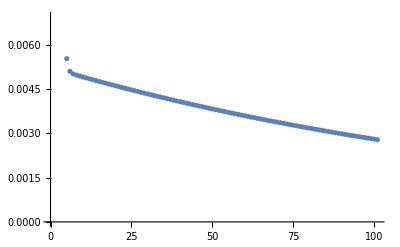

```mathematica
losses0=optimize[loss,grad,w0,IdentityMatrix[2],.15];
ListPlot@losses0
```

#### Exact Hessian as preconditioner

```mathematica
hess=D[loss[{{x,y}}],{{x,y},2}];
hess//MatrixForm
```

(2.06949 | 2.05021
2.05021 | 2.07239)

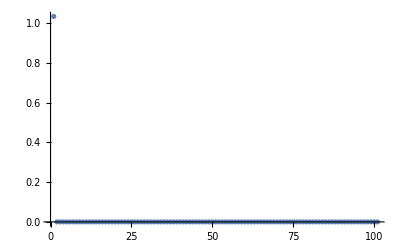

```mathematica
losses1=optimize[loss,grad,w0,Inverse@hess,1.];
ListPlot@losses1
```

#### Cholesky derived preconditioner

```mathematica
pre=Tᵀ.Inverse[Subscript[D, 1].Subscript[D, 1]].T/2;
losses2=optimize[loss,grad,w0,pre,1.];
ListPlot@losses2
```

-Graphics-

### Generate data for TF test

```mathematica
Export["~/git/whitening/exp/linear-cholesky-XY.csv",XY];
Export["~/git/whitening/exp/linear-cholesky-losses0.csv",losses0];
Export["~/git/whitening/exp/linear-cholesky-losses1.csv",losses1];
Export["~/git/whitening/exp/linear-cholesky-losses2.csv",losses2];
Export["~/git/whitening/exp/linear-cholesky-T.csv",T];
Export["~/git/whitening/exp/linear-cholesky-D1.csv",Subscript[D, 1]];
Export["~/git/whitening/exp/linear-cholesky-pre.csv",pre];
```

```mathematica
losses0[[;;10]]
```

{1.03475,0.155254,0.0270041,0.00827915,0.00552226,0.00509353,0.00500441,0.00496496,0.00493292,0.00490212}

```mathematica
losses1[[;;10]]
```

{1.03475,4.90422×10^-28,0.,0.,0.,0.,0.,0.,0.,0.}